### Figure 4

```mathematica
ClearAll["Global`*"]
$Assumptions={g>0,βc>0,βh>0,ΔEh>0,ΔEc>0,γ>0,τd>0};
H=IdentityMatrix[4];
H[[1,1]]=-ΔEh/2;
H[[2,2]]=-ΔEc/2;
H[[3,3]]=ΔEc/2;
H[[4,4]]=ΔEh/2;
σ=DiagonalMatrix[{1,0,1},-1];
Hd=-g/2(σ+Transpose[σ]);
σh=DiagonalMatrix[{1},3];
σc=DiagonalMatrix[{0,1,0},1];
Π[n_]:=DiagonalMatrix[{KroneckerDelta[1,n],KroneckerDelta[2,n],KroneckerDelta[3,n],KroneckerDelta[4,n]}];
Ud=MatrixExp[-I τd Hd];
Udd=MatrixExp[I τd Hd];
Ud1=Series[Ud,{τd,0,1}]//Normal;
Udd1=Series[Udd,{τd,0,1}]//Normal;
Ed[r_]=Series[Ud.r.Udd,{τd,0,2}]//Normal;
Dop[A_,r_]=A.r.ConjugateTranspose[A]-1/2 ConjugateTranspose[A].A.r-1/2 r.ConjugateTranspose[A].A;
Eh[r_]=r+4γ  τd( Dop[σh,r]+Exp[-βh ΔEh]Dop[Transpose[σh],r]);
Ec[r_]=r+4γ  τd( Dop[σc,r]+Exp[-βc ΔEc]Dop[Transpose[σc],r]);
Edec[r_]=Sum[Π[n].r.Π[n],{n,1,4}];
τ[β_]=MatrixExp[- β H]/Tr[MatrixExp[- β H]];
Eh[τ[βh]]-τ[βh]//Simplify
Ec[τ[βc]]-τ[βc]//Simplify
Cycle[r_]=Ed@Eh@Ed@Ec[r];
ρ=DiagonalMatrix[{p1,p2,p3,p4}];
ρ[[1,2]]=x1+I y1;ρ[[2,1]]=x1-I y1;
ρ[[3,4]]=x2+I y2;ρ[[4,3]]=x2-I y2;
ρ1=Series[Cycle[ρ],{τd,0,1}]//Normal;
ρcl= DiagonalMatrix[{p1,p2,p3,p4}];
ρa=Edec@Ed@Edec@Ec[ρcl];
ρ1Cl=Edec@Ed@Edec@Eh[ρa];
St=Solve[(ρ1==ρ)/.p1->(1-p2-p3-p4)//Simplify,{x1,y1,x2,y2,p2,p3,p4}];
StCl=Solve[(ρ1Cl)==ρcl/.p1->(1-p2-p3-p4)//Simplify,{p2,p3,p4}];
ρSt=ρ/.p1->(1-p2-p3-p4)/.First@St//FullSimplify;
ρStCl = ρcl/.p1->(1-p2-p3-p4)/.First@StCl//FullSimplify;
W1=Tr[H.(Ed@Ec[ρSt]-Ec[ρSt])]//Simplify;
W2=Tr[H.(Ed@Eh@Ed@Ec[ρSt]-Eh@Ed@Ec[ρSt])]//Simplify;
W1cl=Tr[H.(Edec@Ed@Edec@Ec[ρStCl]-Edec@Ec[ρStCl])]//Simplify;
W2cl=Tr[H.(ρStCl-Eh@Edec@Ed@Edec@Ec[ρStCl])]//Simplify;
Ωd=Udd.H.Ud-H//Simplify;
EV=Eigenvectors[Ωd];ev=Eigenvalues[Ωd];
ΠΩ=Table[IdentityMatrix[4],{n,1,4}];ω=Table[1,{n,1,4}];
For[n=1,n<5,n++,ΠΩ[[n]]=(Transpose[{EV[[n]]}].Conjugate[{EV[[n]]}])/Tr[Conjugate[{EV[[n]]}].Transpose[{EV[[n]]}]];ω[[n]]=ev[[n]];]
Ewom[r_]=Sum[Tr[ΠΩ[[n]].r]*ΠΩ[[n]],{n,1,4}];
PTPM[i_,j_]=Tr[Π[j].Ed[Π[i].Ec[ρSt].Π[i]]];
WTPM=Sum[Sum[(H[[j,j]]-H[[i,i]])PTPM[i,j],{i,1,4}],{j,1,4}];
VTPM=Sum[Sum[(H[[j,j]]-H[[i,i]])^2PTPM[i,j],{i,1,4}],{j,1,4}]-WTPM^2;
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(*FrameTicks->{{Table[{-k 5/10^4,ScientificForm[-k 5/10^4//N]},{k,0,3}],None}*)
```

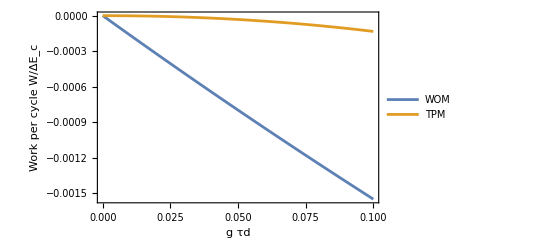

```mathematica
Paru={βh->0.2,βc->1,ΔEh->2,ΔEc->1,γ-> g,τd->u/g,g->0.00001};
ρc=Ec[ρSt];
styleoptions=Sequence@@{LabelStyle->Directive[Black,Background->White,FontSize->14],AspectRatio->0.6,Background->White};    
Plot[{Tr[Ωd.ρc]//.Paru,WTPM//.Paru},{u,0,0.1},Frame->{{True,True},{True,True}},FrameTicksStyle->Directive[Gray,FontColor->Black],FrameTicks->{{True,None},{True,None}},FrameLabel->{{"Work per cycle W/ΔE_c" ,None},{"g τd",None}},PlotLegends->Placed[LineLegend[{"WOM","TPM"},LegendFunction->(Framed[Style[#]]&)],{0.18,0.21}],Evaluate[styleoptions]]
```

C:\Users\elouard1\Nextcloud\Sync\TPM epsilon\Figures\Fig4_b.pdf

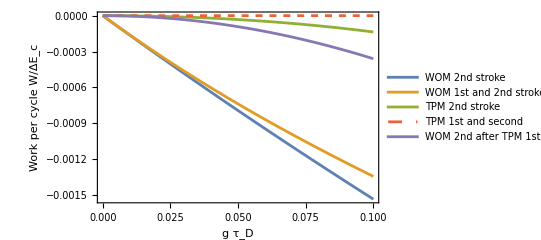

```mathematica
Par={βh->0.2,βc->1,ΔEh->2,ΔEc->1,γ-> g,g->0.00001};
W2 = Tr[Ωd.Eh[Ed[Ec[ρSt]]]]/.τd-> u/g//.Par;
W2p=Tr[Ωd.Eh[Ed[Ewom[Ec[ρSt]]]]]/.τd-> u/g//.Par;
PTPM2[i_,j_]=Tr[Π[j].Ed[Π[i].Eh[Ed[Ec[ρSt]]].Π[i]]];
WTPM2=Sum[Sum[(H[[j,j]]-H[[i,i]])PTPM2[i,j],{i,1,4}],{j,1,4}]/.τd-> u/g//.Par;
PTPM21[i_,j_]=Tr[Π[j].Ed[Π[i].Eh[Sum[Π[l].Ed[Sum[Π[k].Ec[ρSt.Π[k]],{k,1,4}]].Π[l],{l,1,4}]]].Π[i]];
WTPM21=Sum[Sum[(H[[j,j]]-H[[i,i]])PTPM21[i,j],{i,1,4}],{j,1,4}]/.τd-> u/g//.Par;
W2t1=Tr[Ωd.Eh[Ed[Edec[Ec[ρSt]]]]]/.τd-> u/g//.Par;
styleoptions=Sequence@@{LabelStyle->Directive[Black,Background->White,FontSize->16],AspectRatio->0.6,Background->White};    
f4b=Plot[{W2,W2p,WTPM2,WTPM21,W2t1},{u,0,0.1},Frame->{{True,True},{True,True}},FrameTicksStyle->Directive[Gray,FontColor->Black],FrameTicks->{{True,None},{True,None}},FrameLabel->{{"Work per cycle W/ΔE_c",None},{"g τ_D",None}},PlotStyle-> {Automatic,Automatic,Automatic,Dashed},PlotRange->All,PlotLegends->Placed[LineLegend[{"WOM 2nd stroke", "WOM 1st and 2nd strokes","TPM 2nd stroke", "TPM 1st and second","WOM 2nd after TPM 1st"},LegendFunction->(Framed[Style[#]]&)],{Below,Left}],Evaluate[styleoptions]];
Export["C:\\Users\\elouard1\\Nextcloud\\Sync\\TPM epsilon\\Figures\\Fig4_b.pdf",f4b]
Show[f4b]
```

```mathematica
CycleWOM[r_]:=Ed@Ewom[Eh@Ed@Ewom[Ec[r]]];
ρ2=Series[CycleWOM[ρ],{τd,0,1}]//Normal;
St2=Solve[(ρ2==ρ)/.p1->(1-p2-p3-p4)//Simplify,{x1,y1,x2,y2,p2,p3,p4}];
ρSt2=ρ/.p1->(1-p2-p3-p4)/.First@St2//FullSimplify;
CycleTPM[r_]:=Ed@Edec[Eh@Ed@Edec[Ec[r]]];
ρTPM=Series[CycleTPM[ρ],{τd,0,2}]//Normal;
StTPM=Solve[(ρTPM==ρ)/.p1->(1-p2-p3-p4)//Simplify,{x1,y1,x2,y2,p2,p3,p4}];
ρStTPM=ρ/.p1->(1-p2-p3-p4)/.First@St2//FullSimplify;
Paru={βh->0.2,βc->1,ΔEh->4,ΔEc->1,γ->u g,τd->6,g->0.0001};
W1γ = Tr[Ωd.Ec[ρSt]]//.Paru;
W2γ = Tr[Ωd.Eh[Ed[Ec[ρSt]]]]//.Paru;
W12γ=Tr[Ωd.(Ec[ρSt2])]//.Paru;
W22γ=Tr[Ωd.(Eh@Ed@Ewom[Ec[ρSt2]])]//.Paru;
PTPM[i_,j_]=Tr[Π[j].Ed[Π[i].Ec[ρStTPM].Π[i]]];
WTPMγ=Sum[Sum[(H[[j,j]]-H[[i,i]])PTPM[i,j],{i,1,4}],{j,1,4}]//.Paru;
PTPM21[i_,j_]=Tr[Π[j].Ed[Π[i].Eh[Sum[Π[l].Ed[Sum[Π[k].Ec[ρStTPM.Π[k]],{k,1,4}]].Π[l],{l,1,4}]]].Π[i]];
WTPM21γ=Sum[Sum[(H[[j,j]]-H[[i,i]])PTPM21[i,j],{i,1,4}],{j,1,4}]//.Paru;
```

```mathematica
asp=0.6;
styleoptions=Sequence@@{LabelStyle->Directive[Black,Background->White,FontSize->16],AspectRatio->asp,Background->White};    
p1=Plot[{(W1γ+W2γ),(W12γ+W22γ),(WTPM21γ+WTPMγ)},{u,0.,0.1},PlotRange->All,Frame->{{True,True},{True,True}},FrameTicksStyle->Directive[Gray,FontColor->Black],FrameTicks->{{True,None},{True,None}},FrameLabel->{{"Work per cycle W/ΔE_c",None},{"γ/g",None}},PlotStyle->{Automatic,Automatic,Dashed},Evaluate[styleoptions],PlotLegends->Placed[LineLegend[{"Unmeasured steady state + WOM","WOM steady state + WOM","TPM steady state + TPM"},LegendFunction->(Framed[Style[#]]&),LegendLayout->"Column"],Below]];
styleI=Sequence@@{LabelStyle->Directive[Black,Background->Transparent,FontSize->14],AspectRatio->0.6,Background->Transparent};
p2=Plot[{(W12γ+W22γ),(WTPM21γ+WTPMγ)},{u,0,0.1},PlotRange->All,Frame->{{True,True},{True,True}},FrameTicksStyle->Directive[Gray,FontColor->Black],FrameTicks->{{{-1/10^12//N,-2/10^12//N},None},{None,None}},PlotStyle->{Automatic,Automatic,Dashed},Evaluate[styleI]];
```

C:\Users\elouard1\Nextcloud\Sync\TPM epsilon\Figures\Fig4_c.pdf

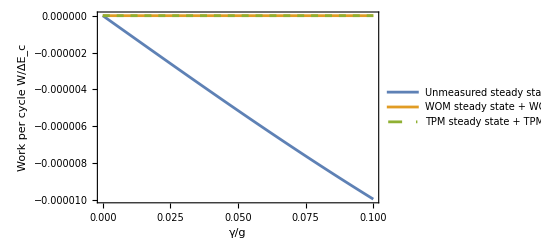

```mathematica
f1=Show[p1,Epilog->{Inset[p2,{0.068,-2.5/10^6},Automatic,Scaled[0.6]]}];
Export["C:\\Users\\elouard1\\Nextcloud\\Sync\\TPM epsilon\\Figures\\Fig4_c.pdf",f1]
Show[f1]
```

## Figure 5

```mathematica
ClearAll["Global`*"]
$Assumptions={ω>0,ωp>0};
sp={{0,1},{0,0}};sm=Transpose[sp];sx=sp+sm;sy=I(sm-sp);sz=sp.sm-sm.sp;id=sz.sz;
U = MatrixExp[ -I(θ sy/2)];Ud = MatrixExp[ I (θ/2 sy)];
H=ω/2(id+sz);Hp=ωp/2(id+sz);τ=MatrixExp[-β H]/Tr[MatrixExp[-β H]]//Simplify;
Ω = Ud.Hp.U-H//FullSimplify;
ev=Eigenvalues[Ω];
EV=(ωp Eigenvectors[Ω]//Simplify);
bp={EV[[2]]};kp=Transpose[bp];bm={EV[[1]]};km=Transpose[bm];
Πp=(kp.bp)/Tr[bp.kp]//Simplify;
Πm=(km.bm)/Tr[bm.km]//Simplify;
Ωp=ev[[2]];
Ωm=ev[[1]];
```

```mathematica
pp=Tr[τ.Πp];
pm=Tr[τ.Πm];
W= pm Ωm;
ρf= Πp.τ.Πp+ U.Πm.τ.Πm.Ud;QH=Tr[H.(τ-ρf)];
QC= (pp Log[pp]+pm Log[pm])/βC;
Wres=-QC;
Wmeas = Tr[( Πp.τ.Πp+ Πm.τ.Πm-τ).H];
η=(-(W+Wres+Wmeas))/QH;
Π1={{1,0},{0,0}};p1=τ[[1,1]];Π0={{0,0},{0,1}};
WMD = p1 Tr[H.(U.Π1.Ud-Π1)];
WMDres= (-p1 Log[p1]-(1-p1)Log[1-p1])/βC;
ρfMF = U.Π1.τ.Π1.Ud+Π0.τ.Π0;
ηMD=(-(WMD+WMDres))/Tr[H.(τ-ρfMF)];
parβ={ωp->ω,ω->1,θ->π/3,β->u,βC->10};
```

C:\Users\elouard1\Nextcloud\Sync\TPM epsilon\Figures\Fig5_a.pdf

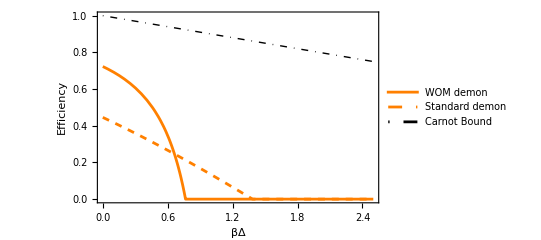

```mathematica
styleoptions=Sequence@@{LabelStyle->Directive[Black,Background->White,FontSize->14],AspectRatio->0.6,Background->White};
f5a=Plot[{η HeavisideTheta[-W-Wres-Wmeas]//.parβ,ηMD HeavisideTheta[-WMD-WMDres]//.parβ,1-β/βC//.parβ},{u,0,2.5},PlotRange->{0,1},PlotStyle->{Orange,{Orange,Dashed},{Black,DotDashed,Thick}},PlotLegends->Placed[LineLegend[{"WOM demon","Standard demon","Carnot Bound"},LegendFunction->(Framed[Style[#]]&)],{0.68,0.45}],Axes->True,Frame->{{True,True},{True,True}},FrameTicksStyle->Directive[Gray,FontColor->Black],FrameTicks->{{True,None},{True,None}},FrameLabel->{{"Efficiency",None},{"βΔ",None}},Evaluate[styleoptions]];
Export["C:\\Users\\elouard1\\Nextcloud\\Sync\\TPM epsilon\\Figures\\Fig5_a.pdf",f5a]
Show[f5a]
```

C:\Users\elouard1\Nextcloud\Sync\TPM epsilon\Figures\Fig5_b.pdf

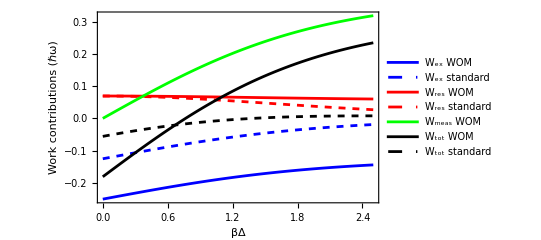

```mathematica
styleoptions=Sequence@@{LabelStyle->Directive[Black,Background->White,FontSize->20],AspectRatio->0.6,Background->White};
f5b=Plot[{W//.parβ,WMD//.parβ,Wres//.parβ,WMDres//.parβ,Wmeas//.parβ,W+Wres+Wmeas//.parβ,WMD+WMDres//.parβ},{u,0,2.5},(*PlotLegends->{"W_ex WOM demon","W_ex standard","W_res WOM demon", "W_res standard","W_meas WOM","W_tot WOM","W_tot standard"},*)PlotLegends->Placed[LineLegend[{"W_ex WOM","W_ex standard","W_res WOM", "W_res standard","W_meas WOM","W_tot WOM","W_tot standard"},LegendFunction->(Framed[Style[#]]&),LegendLayout->"Row"],{Below,Left}],PlotStyle->{Blue,{Blue,Dashed},Red,{Red,Dashed},Green,Black,{Black, Dashed}},Evaluate[styleoptions],(*AxesLabel->{"βΔ","Work contributions (ℏω)"},*)Axes->True,Frame->{{True,True},{True,True}},FrameTicksStyle->Directive[Gray,FontColor->Black],FrameTicks->{{True,None},{True,None}},FrameLabel->{{"Work contributions (ℏω)",None},{"βΔ",None}}];
Export["C:\\Users\\elouard1\\Nextcloud\\Sync\\TPM epsilon\\Figures\\Fig5_b.pdf",f5b]
Show[f5b]
```